```mathematica
RandomGoodRule[K_:2, R_:1]:=(
rca=ResourceFunction["RandomCellularAutomatonRule"];

GoodRuleCondition[rule_]:=If[Length[Last[CellularAutomaton[rule, {RandomInteger[K-1, 100], 0}, 100]]]>150, False, With[{l=Table[Length[StripZeros[CellularAutomaton[rule, {RandomInteger[K-1, 100], 0}, {{{100}}}]]], 10]}, Mean[l]<100&&Min[l]==0&&Max[l]<150&&Max[l]>0]];

ParallelTry[If[GoodRuleCondition[#], #, $Failed]&,ParallelTable[{rca[{K, R}, "Quiescent"->True, "Type"->"Symmetric"]["RuleNumber"], K, R}, 10000]]
);

RandomGoodTotalisticRule[K_:2, R_:1]:=(
rca=ResourceFunction["RandomCellularAutomatonRule"];

GoodRuleCondition[rule_]:=If[Length[Last[CellularAutomaton[rule, {RandomInteger[K-1, 100], 0}, 100]]]>150, False, With[{l=Table[Length[StripZeros[CellularAutomaton[rule, {RandomInteger[K-1, 100], 0}, {{{100}}}]]], 10]}, Mean[l]<100&&Min[l]==0&&Max[l]<150&&Max[l]>0]];

ParallelTry[If[GoodRuleCondition[#], #, $Failed]&,ParallelTable[{rca[{K, R}, "Quiescent"->True, "Type"->"Totalistic"]["TotalisticCode"], {K, 1}, R}, 10000]]
);
```

```mathematica
version=2;

rule={20, {2, 1}, 2};
rule={1329, {3, 1}, 1};
rule={123213344, 4, 2}; 
(* rule={1802174068386, 3};  *)
(* rule={52, {2, 1},2};


rule={20, {2, 1}, 2}; *)
rule={1329, {3, 1}, 1};
(* rule={52, {2, 1},2}; *)
rule={1326, {3, 1}, 1};

rule={7492516167169308646368004455659429445327030305892293894816880501426633766203150235235080168693170352598475183825783,3,2};
(*  rule=RandomGoodTotalisticRule[3, 2] *)
rule = {20, {2, 1}, 2}

rule={1329, {3, 1}, 1};
```

{20,{2,1},2}

```mathematica
helperFile=Import[NotebookDirectory[]<>"kernels/helper.cl"];
templateFile=Import[NotebookDirectory[]<>"kernels/template_v"<>ToString[version]<>".cl", "Text"];
filledTemplateFile=templateFile;
```

```mathematica
TemplateReplace[rule_]:=(filledTemplateFile=StringReplace[filledTemplateFile,rule];)
```

```mathematica
Clear[StrongAssert]
StrongAssert[test_, messages__]:=If[!test, Print[messages]; Quit[4]]
SetAttributes[StrongAssert, HoldRest]
```

```mathematica
Clear[f]
f[formatString_String, args___]:=Module[{str=formatString, arglist={args}},
Do[str=StringReplace[str, "``"->ToString[arglist[[i]]],1], {i, Length[arglist]}]; str]

Clear[StringJoinTable]
StringJoinTable[args___]:=StringJoin[Table[args]]
SetAttributes[StringJoinTable, HoldAll]
```

```mathematica
PointApplyRule[rule_,init_]:=CellularAutomaton[rule, init, 1][[2,(Length[init]+1)/2]]

Clear[AnalyzeRule];
AnalyzeRule[{n_, k_, r_}]:=AnalyzeRule[{n, k, r}]=Module[{rule={n,k, r}},<|
"Rule"->rule, (* may be overrided by a totalistic rule *)
"NormalRule"->rule,  (* always {booleanfunctionnumber, colors, radius} *)
"Colors"->k,
"Radius"->r,
"Totalistic"->False,
"Number"->n,
"Quiescent"->Not[Positive[PointApplyRule[rule, ConstantArray[0, 2r+1]]]],
"Symmetric"->AllTrue[Tuples[Range[0, k-1], 2r+1], PointApplyRule[rule, #]==PointApplyRule[rule, Reverse[#]]&]
|>]

AnalyzeRule[{n_, {k_, 1}, r_}]:=AnalyzeRule[{n, {k, 1}, r}]=With[
{rule={n, {k, 1}, r}},{num=FromDigits[Reverse[PointApplyRule[rule, #]&/@Tuples[Range[0, k-1], 2r+1]], k]},
Join[AnalyzeRule[{num, k, r}],<|"Rule"->rule, "Totalistic"->True|>]
]
AnalyzeRule[{n_, k_}]:=AnalyzeRule[{n, k, 1}]
AnalyzeRule[{n_}]:=AnalyzeRule[{n, 2}]
AnalyzeRule[n_]:=AnalyzeRule[{n}]
```

```mathematica
ar=AnalyzeRule[rule]

n=ar["Number"];
k=ar["Colors"];
r=ar["Radius"];

ArrayPlot[CellularAutomaton[{n, k, r}, {RandomInteger[k-1, 100], 0}, 300], ImageSize->Small]
```

<|Rule→{1329,{3,1},1},NormalRule→{4753971678840,3,1},Colors→3,Radius→1,Totalistic→True,Number→4753971678840,Quiescent→True,Symmetric→True|>

-Graphics-

```mathematica
StrongAssert[ar["Quiescent"], "Rule Not Quiescent"]
```

```mathematica
MinimalBooleanForm[bf_]:=First[MinimalBy[
Join[
ParallelMap[TimeConstrained[(Replace[FullSimplify[First[BooleanMinimize[bf, #]]],Implies[a_,b_]->Or[Not[a], b], All]), 5, BooleanConvert[bf, "CNF"]]&,{"DNF","CNF","ANF", "AND", "OR"}], (* FullSimplify[First[BooleanConvert[bf, #]]]&/@{"ESOP", "NOR2", "NAND2", "BDT"} *){}
], 
VertexCount@*ExpressionTree]]

ConvertExprToString[expr_]:=StringReplace[f["``",StringReplace[ToString[expr, TraditionalForm],{"∧"->"&", "∨"->"|", "¬"->"~", "⊻"->" ^ ", " "->"", "False"->"0"}]], {"~ "->"~"}]
```

```mathematica
bits=BitLength[k-1]
```

2

```mathematica
Clear[Bits]
Bits[n_Integer, len_Integer:64]:=IntegerDigits[n, 2, len]
Bits[n_List, len_Integer:64]:=IntegerDigits[#, 2, len]&/@n
```

## Update Rule

```mathematica
fullUpdateRule=Catenate[Bits[#, bits]]->Bits[PointApplyRule[rule, #], bits]&/@Tuples[Range[0, k-1], 2r+1]
```

{{0,0,0,0,0,0}→{0,0},{0,0,0,0,0,1}→{1,0},{0,0,0,0,1,0}→{0,0},{0,0,0,1,0,0}→{1,0},{0,0,0,1,0,1}→{0,0},{0,0,0,1,1,0}→{0,1},{0,0,1,0,0,0}→{0,0},{0,0,1,0,0,1}→{0,1},{0,0,1,0,1,0}→{0,1},{0,1,0,0,0,0}→{1,0},{0,1,0,0,0,1}→{0,0},{0,1,0,0,1,0}→{0,1},{0,1,0,1,0,0}→{0,0},{0,1,0,1,0,1}→{0,1},{0,1,0,1,1,0}→{0,1},{0,1,1,0,0,0}→{0,1},{0,1,1,0,0,1}→{0,1},{0,1,1,0,1,0}→{1,0},{1,0,0,0,0,0}→{0,0},{1,0,0,0,0,1}→{0,1},{1,0,0,0,1,0}→{0,1},{1,0,0,1,0,0}→{0,1},{1,0,0,1,0,1}→{0,1},{1,0,0,1,1,0}→{1,0},{1,0,1,0,0,0}→{0,1},{1,0,1,0,0,1}→{1,0},{1,0,1,0,1,0}→{0,1}}

```mathematica
o1=MinimalBooleanForm/@BooleanFunction[fullUpdateRule][[1, All, 0]]
```

{(!#2&&((#1&&((!#5&&#3&&#6)||(!#3&&#4&&#5)))||(!#1&&!#3&&!(#4&&#6)&&(#4||#6)&&!#5)))||(!#1&&#2&&((#3&&#5)||(!#3&&!#4&&!#5&&!#6))),!(#1&&#2)&&!(#1&&#3&&#6)&&(!#1||#3||!#4||!#5)&&(#1||#2||#3||#4)&&(#1||#2||#3||#5)&&(#1||#2||#5||#6)&&(#1||#3||#4||#5)&&(#1||#3||#5||#6)&&!(#2&&#3&&#5)&&(#3||#4||#5||#6)}

```mathematica
o2=Table[ConvertExprToString[expr/.Table[Slot[i]->"a"<>ToString[i], {i,bits*(2r+1)}]], {expr, o1}]
```

{(~a2 & ((a1 & ((~a5 & a3 & a6) | (~a3 & a4 & a5))) | (~a1 & ~a3 & ~(a4 & a6) & (a4 | a6) & ~a5))) | (~a1 & a2 & ((a3 & a5) | (~a3 & ~a4 & ~a5 & ~a6))),~(a1 & a2) & ~(a1 & a3 & a6) & (~a1 | a3 | ~a4 | ~a5) & (a1 | a2 | a3 | a4) & (a1 | a2 | a3 | a5) & (a1 | a2 | a5 | a6) & (a1 | a3 | a4 | a5) & (a1 | a3 | a5 | a6) & ~(a2 & a3 & a5) & (a3 | a4 | a5 | a6)}

```mathematica
o3=StringRiffle[Table[f["u256_shl((``) & NTHBITSMASK, ``)", o2[[i]], bits-i], {i, bits}], " | "]
If[bits==1, o3=First[o2]]
```

u256_shl(((~a2 & ((a1 & ((~a5 & a3 & a6) | (~a3 & a4 & a5))) | (~a1 & ~a3 & ~(a4 & a6) & (a4 | a6) & ~a5))) | (~a1 & a2 & ((a3 & a5) | (~a3 & ~a4 & ~a5 & ~a6)))) & NTHBITSMASK, 1) | u256_shl((~(a1 & a2) & ~(a1 & a3 & a6) & (~a1 | a3 | ~a4 | ~a5) & (a1 | a2 | a3 | a4) & (a1 | a2 | a3 | a5) & (a1 | a2 | a5 | a6) & (a1 | a3 | a4 | a5) & (a1 | a3 | a5 | a6) & ~(a2 & a3 & a5) & (a3 | a4 | a5 | a6)) & NTHBITSMASK, 0)

```mathematica
preprereqs=f["    u256 o = *oPoint;\n"];

prereqs=StringJoinTable[f[Which[Positive[i-bits],"    u256 a`` = u256_shl(o, ``);\n", Negative[i-bits], "    u256 a`` = u256_shr(o, ``);\n", True,"    u256 a`` = o;\n"], i, Abs[i-bits]], {i, (2r+1)*bits}];

updateFunction=f["static inline void update256(u256 *restrict oPoint) {
    u256 o = *oPoint;

``
    *oPoint = ``;
}\n",prereqs, o3 ]

TemplateReplace["TEMPLATE_update256"->updateFunction]
```

static inline void update256(u256 *restrict oPoint) {
    u256 o = *oPoint;

    u256 a1 = u256_shr(o, 1);
    u256 a2 = o;
    u256 a3 = u256_shl(o, 1);
    u256 a4 = u256_shl(o, 2);
    u256 a5 = u256_shl(o, 3);
    u256 a6 = u256_shl(o, 4);

    *oPoint = u256_shl(((~a2 & ((a1 & ((~a5 & a3 & a6) | (~a3 & a4 & a5))) | (~a1 & ~a3 & ~(a4 & a6) & (a4 | a6) & ~a5))) | (~a1 & a2 & ((a3 & a5) | (~a3 & ~a4 & ~a5 & ~a6)))) & NTHBITSMASK, 1) | u256_shl((~(a1 & a2) & ~(a1 & a3 & a6) & (~a1 | a3 | ~a4 | ~a5) & (a1 | a2 | a3 | a4) & (a1 | a2 | a3 | a5) & (a1 | a2 | a5 | a6) & (a1 | a3 | a4 | a5) & (a1 | a3 | a5 | a6) & ~(a2 & a3 & a5) & (a3 | a4 | a5 | a6)) & NTHBITSMASK, 0);
}

## Constants

```mathematica
tohex=Dispatch[{"10"->"A", "11"->"B", "12"->"C", "13"->"D", "14"->"E", "15"->"F"}];
NumberAsHexString[i_Integer]:=StringJoin["0x",(ToString/@IntegerDigits[i, 16, 16])/.tohex,"ULL"]
```

```mathematica
bitstemplate=f["#define BITS ``\n", bits];
TemplateReplace["TEMPLATE_BITS"->bitstemplate]
```

```mathematica
ktemplate=f["#define K ``\n", k];
TemplateReplace["TEMPLATE_K"->ktemplate]
```

```mathematica
rtemplate=f["#define R ``\n", r];
TemplateReplace["TEMPLATE_R"->rtemplate]
```

```mathematica
symmetrictemplate=f["#define SYMMETRIC ``\n", Boole[ar["Symmetric"]]];
TemplateReplace["TEMPLATE_SYMMETRIC"->symmetrictemplate]
```

```mathematica
topmostbitmask=f["#define TOPMOSTBITSMASK ``\n", NumberAsHexString[FromDigits[Table[Boole[i<=bits*(2r+1)], {i, 64}], 2]]];
TemplateReplace["TEMPLATE_TOPMOSTBITSMASK"->topmostbitmask]
```

```mathematica
bottommostbitsmask=f["#define BOTTOMMOSTBITSMASK ``\n", NumberAsHexString[FromDigits[Reverse@Table[Boole[i<=r+1], {i, 64}], 2]]];
TemplateReplace["TEMPLATE_BOTTOMMOSTBITSMASK"->bottommostbitsmask]
```

```mathematica
bottombitsmask=f["#define BOTTOMBITSMASK ``\n", NumberAsHexString[BitShiftLeft[1, bits]-1]];
TemplateReplace["TEMPLATE_BOTTOMBITSMASK"->bottombitsmask]
```

```mathematica
bottombitsmask
```

#define BOTTOMBITSMASK 0x0000000000000003ULL

```mathematica
nthbitmask=f["#define NTHBITSMASK (u256)(``)",StringRiffle[StringJoin["0x",#, "ULL"]&/@Partition[ToString/@IntegerDigits[FromDigits[Flatten[ConstantArray[Reverse@UnitVector[bits, 1], Ceiling[256/bits]]][[;;256]], 2], 16]/.tohex, 16], ", "]];

InputForm[nthbitmask]
```

"#define NTHBITSMASK (u256)(0x5555555555555555ULL, 0x5555555555555555ULL, 0x5555555555555555ULL, 0x5555555555555555ULL)"

```mathematica
TemplateReplace["TEMPLATE_NTHBITSMASK"->nthbitmask]
```

## Other

```mathematica
allowedIntegers=Bits[Range[0, k-1]];
#->Boole[!MemberQ[allowedIntegers, #]]&/@Tuples[{0, 1}, bits]
MinimalBooleanForm[BooleanFunction[%]]
ConvertExprToString[%/.Slot[x_]:>f["(x >> ``)", bits-x]]
validpackedintegertemplate=f["``", %];
InputForm[validpackedintegertemplate]
Head[validpackedintegertemplate]
```

{{0,0}→1,{0,1}→1,{1,0}→1,{1,1}→1}

True

True

String

"True"

```mathematica
TemplateReplace["TEMPLATE_VALID_PACKED_INTEGER"->validpackedintegertemplate]
```

## Output

```mathematica
outputFile=helperFile<>filledTemplateFile;

file=OpenWrite[NotebookDirectory[]<>"kernels/kernel.cl", PageWidth->Infinity];
WriteString[file, outputFile];
Close[file];
```

## Run It

```mathematica
RunProcess[{"bash", "-l", "/home/chris/Programming/GPU/opencl3/run_in_env.sh"}]
```

$Aborted

## Testing

```mathematica
Get["/home/chris/Programming/Wolfram/Summer/DetectPeriodTools.wl"]
```

```mathematica
ConvertFromPackedInt[n_Integer]:=FromDigits[FromDigits[#, 2]&/@Partition[IntegerDigits[n, 2, 256], bits], k]
ConvertFromPackedIntList[n_Integer]:=FromDigits[#, 2]&/@Partition[IntegerDigits[n, 2, 256], bits]
```

```mathematica
RepeatedRotate[list_List, factor_Integer:1]:=Table[RotateRight[list[[i]], 20+factor * i], {i, Length[list]}]
```

```mathematica
ReadOutputFile[]:=Developer`ToPackedArray[ReadList[StringToStream[First[StringCases[StringReplace[Import["/home/chris/Programming/GPU/opencl3/out.txt"], "\n"->""], "{"~~x__~~"}":>ToString[{x}]], "{}"]]][[1]]]
```

```mathematica
Clear[OAArayPlot]
OAArayPlot[stuff__]:=AArrayPlot[rule,ConvertFromPackedIntList[Echo@FromDigits[Join@@Bits[{stuff},64], 2]], 500, ImageSize->{Automatic, 300}]
```

```mathematica
DecentRunLength[init_, default_:500]:=30+2*Length[Union[StripZeros/@RunCA[rule,init, default]]]
```

12

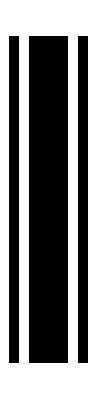
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
out=Rest[Sort[ReadOutputFile[]]];
Length[out]
{AArrayPlot[rule, RandomInteger[k-1, 300]],ParallelMap[Labeled[AArrayPlot[rule, #, DecentRunLength[#, 30]], ClickToCopy[#, {rule,#}]]&,Sort[out[[;;UpTo[10]]]]]}
```

```mathematica
out=Rest[Sort[ReadOutputFile[]]];
Length[out]
outDeduped=FromDigits[#, k]&/@Union[Join@@ParallelTable[SplitSeparateSolutions2[CellularAutomaton[rule, {IntegerDigits[init, k], 0}, 1000][[-100;;]], rule], {init, out}]];
Length[outDeduped]
outDeduped2=DedupSame[Join@@ParallelMap[DetectPeriod[rule, #]&, outDeduped]][[All, "Original"]];
Length[outDeduped2]
ParallelMap[Labeled[AArrayPlot[rule, #, DecentRunLength[#, 300]], ClickToCopy[#]]&,Sort[RandomSample[outDeduped2, UpTo[250]]]]
ParallelMap[Labeled[AArrayPlot[rule, #, DecentRunLength[#, 300]], ClickToCopy[#]]&,Sort[RandomSample[out, UpTo[250]]]]
```

12

12

8

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
rule
```

{20,{2,1},2}